(ⅇ^(-1/8 (-10+x)^2))/(2 √(2 π))+(ⅇ^(-x^2/2))/(√(2 π))

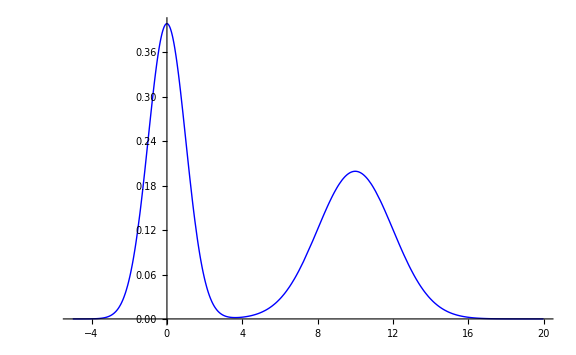

```mathematica
f[x_] = PDF[NormalDistribution[0,1],x]+PDF[NormalDistribution[10,2],x]
Plot[f[x],{x,-5,20},ImageSize->Large,PlotStyle->{{Blue,Thick}}]
```